```mathematica
v=9;
l=50;
vv=ToString[v];
ll=ToString[l];
correlation1[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-susceptibility-1.txt",{Number,Number}];
correlation2[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-susceptibility-2.txt",{Number,Number}];
correlation3[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-susceptibility-3.txt",{Number,Number}];
correlation4[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-susceptibility-4.txt",{Number,Number}];
```

```mathematica
ClearAll[corrtest1,corrtest2]
```

```mathematica
Do[
Do[
vv=ToString[v];
ll=ToString[l];
corrtest1[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-susceptibility-test-1.txt",{Number,Number}];
corrtest2[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9DifferentLengths/v"<>vv<>"-l"<>ll<>"k-susceptibility-test-2.txt",{Number,Number}];
corrtest3[v][l]=Table[{corrtest1[v][l][[All,1]][[i]],corrtest1[v][l][[All,2]][[i]]/(l*1000*corrtest1[v][l][[All,1]][[i]])},{i,1,Length[corrtest1[v][l]]}];
,{v,{5,9}}]
,{l,{5,10,20,30,50}}]
```

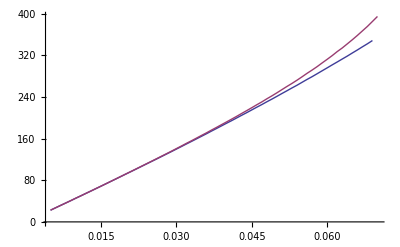

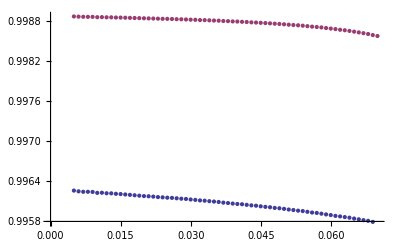

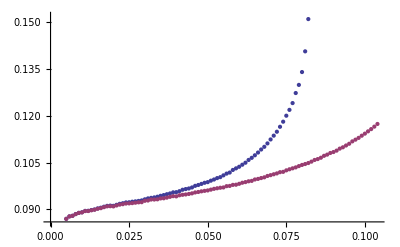

```mathematica
l=50;
ListPlot[{corrtest1[5][l],corrtest1[9][l]},PlotRange->Full,Joined->True]

ListPlot[{corrtest2[5][l],corrtest2[9][l]}]
ListPlot[{corrtest3[9][5],corrtest3[5][5]}]
```

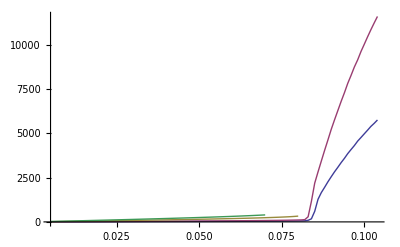

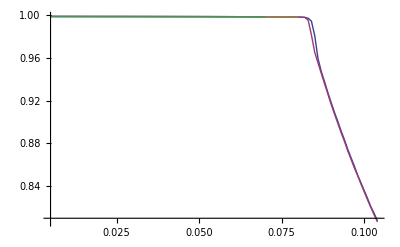

```mathematica
v=9;
ListPlot[{corrtest1[v][5],corrtest1[v][10],corrtest1[v][30],corrtest1[v][50]},PlotRange->Full,Joined->True,PlotLegend->{"5k","10k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{corrtest2[v][5],corrtest2[v][10],corrtest2[v][30],corrtest2[v][50]},PlotRange->Full,Joined->True,PlotLegend->{"5k","10k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

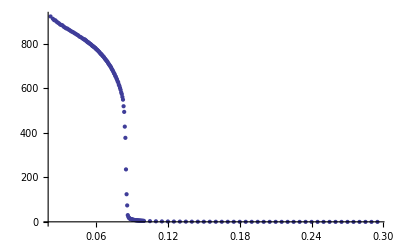

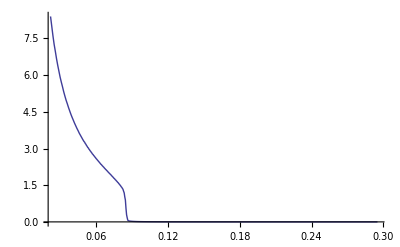

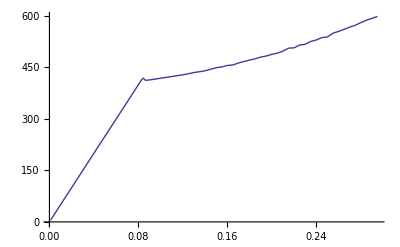

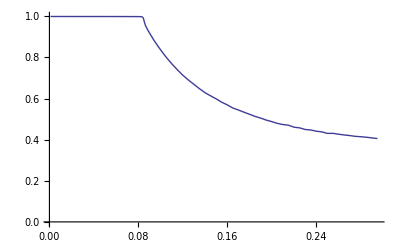

```mathematica
ListPlot[correlation12[l],PlotRange->Full]
ListLinePlot[correlation22[l],PlotRange->Full]
ListLinePlot[correlation32[l],PlotRange->Full]
ListLinePlot[correlation42[l],PlotRange->Full]
```

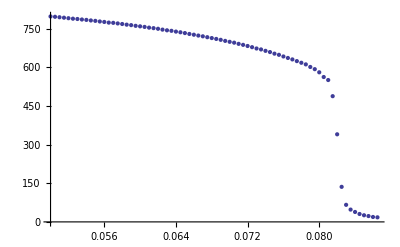

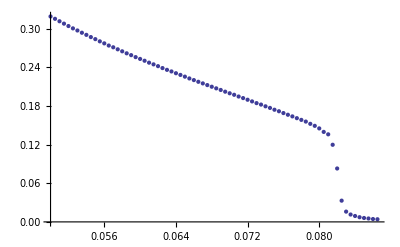

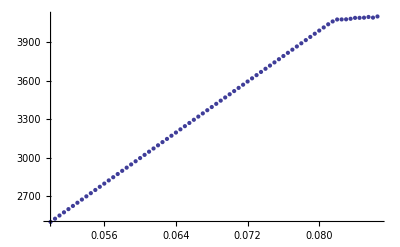

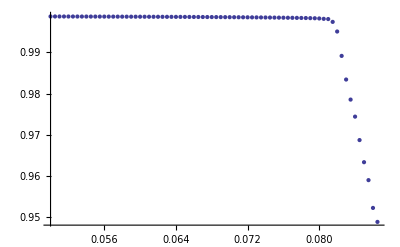

```mathematica
l=50;
ListPlot[correlation1[l],PlotRange->Full]
ListPlot[correlation2[l],PlotRange->Full]
ListPlot[correlation3[l],PlotRange->Full]
ListPlot[correlation4[l],PlotRange->Full]
```

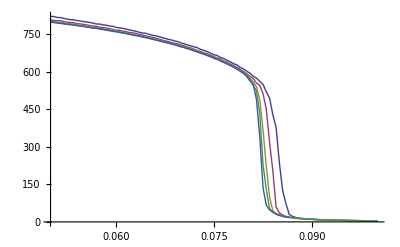

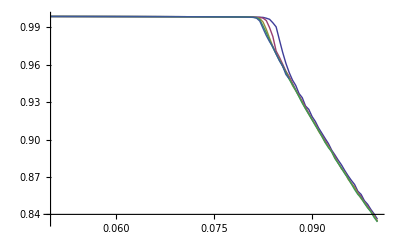

```mathematica
ListLinePlot[{correlation1[5],correlation1[10],correlation1[20],correlation1[30],correlation1[50]},PlotRange->Full]
ListLinePlot[{correlation2[5],correlation2[10],correlation2[20],correlation2[30],correlation2[50]},PlotRange->Full]
ListLinePlot[{correlation3[5],correlation3[10],correlation3[20],correlation3[30],correlation3[50]},PlotRange->Full]
ListLinePlot[{correlation4[5],correlation4[10],correlation4[20],correlation4[30],correlation4[50]},PlotRange->Full]
```

```mathematica
Do[
Do[
vv=ToString[v];
ll=ToString[l];
Chi4[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized.txt",{Number,Number}];
Chi4t[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top.txt",{Number,Number}];
Chi4f[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine.txt",{Number,Number}];
Chi4ft[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine.txt",{Number,Number}];

,{v,{5,7,9}}]
,{l,{5,10,20,30,50,100}}]
Do[
Do[
vv=ToString[v];
ll=ToString[l];
Chi4c[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-complete.txt",{Number,Number}];
Chi4ct[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-complete.txt",{Number,Number}];

,{v,{5,7,9}}]
,{l,{5,10,20,30,50}}]
```

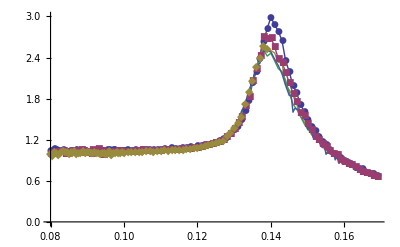

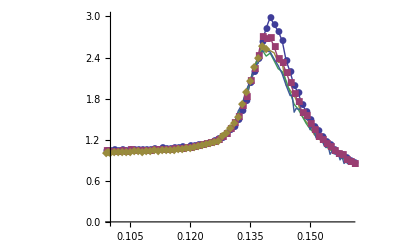

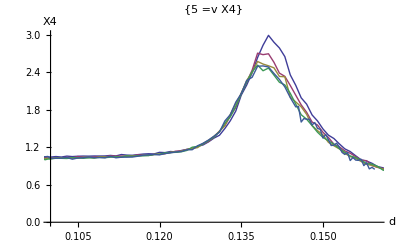

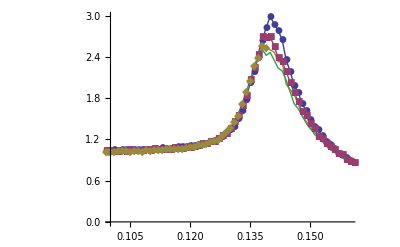

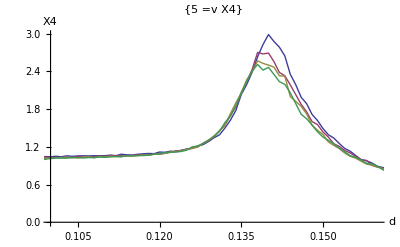

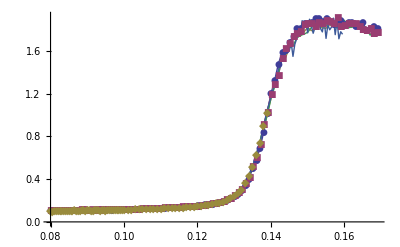

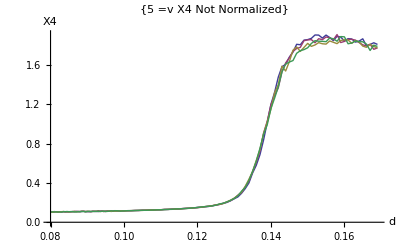

```mathematica
v=5;
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->{Full,{0,3}},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->{{0.1,0.16},{0,3}},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->{{0.1,0.16},{0,3}},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{{0.1,0.16},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{{0.1,0.16},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4ct[v][5],Chi4ct[v][10],Chi4ct[v][20],Chi4ct[v][30],Chi4ct[v][50]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4 Not Normalized" v},PlotLegend->{"5k","10k","20k","30k","50k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"},PlotMarkers->Automatic]
ListPlot[{Chi4ct[v][5],Chi4ct[v][10],Chi4ct[v][20],Chi4ct[v][30]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4 Not Normalized" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
```

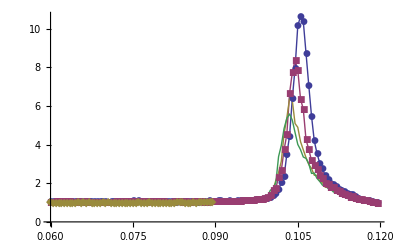

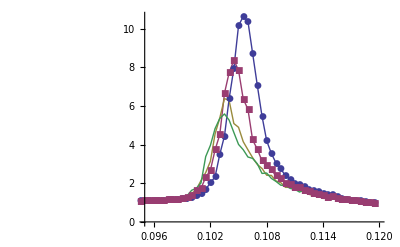

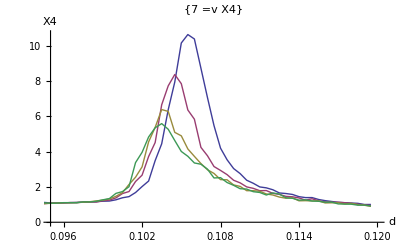

-Graphics-

-Graphics-

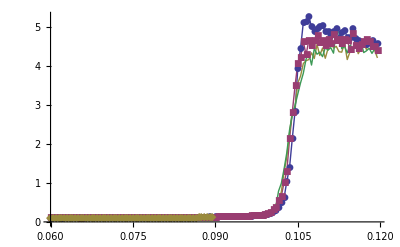

```mathematica
v=7;
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{Full,Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{{0.095,0.12},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{{0.095,0.12},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{{0.095,0.12},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30]},PlotRange->{{0.095,0.12},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4ct[v][5],Chi4ct[v][10],Chi4ct[v][20],Chi4ct[v][30]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4 Not Normalized" v},PlotLegend->{"5k","10k","20k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"},PlotMarkers->Automatic]
ListPlot[{corrtest1[v][50]},PlotRange->Full]
```

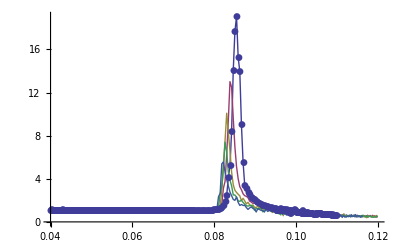

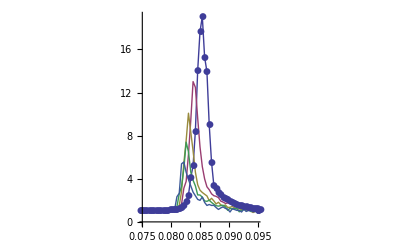

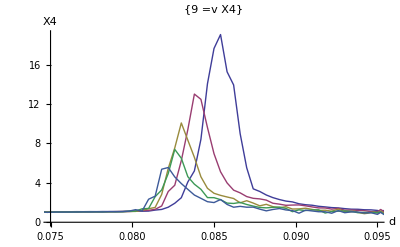

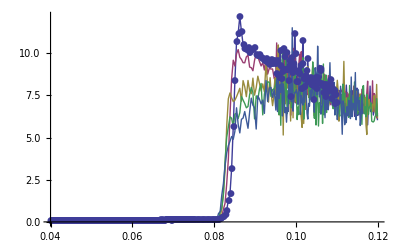

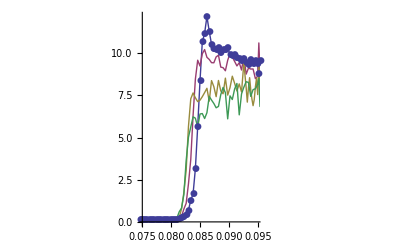

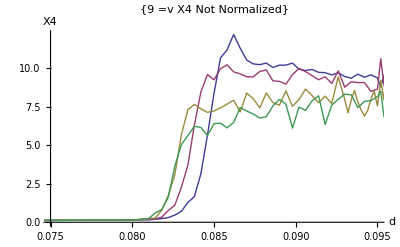

```mathematica
v=9;
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->{{0.075,0.095},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->{{0.075,0.095},Full},Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4ct[v][5],Chi4ct[v][10],Chi4ct[v][20],Chi4ct[v][30],Chi4ct[v][50]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4 Not Normalized" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"},PlotMarkers->Automatic]
ListPlot[{Chi4ct[v][5],Chi4ct[v][10],Chi4ct[v][20],Chi4ct[v][30]},PlotRange->{{0.075,0.095},Full},Joined->True,PlotLabel->{"=v  Χ4 Not Normalized" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"},PlotMarkers->Automatic]
ListPlot[{Chi4ct[v][5],Chi4ct[v][10],Chi4ct[v][20],Chi4ct[v][30]},PlotRange->{{0.075,0.095},Full},Joined->True,PlotLabel->{"=v  Χ4 Not Normalized" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,AxesLabel->{"d","Χ4"}]
```

-Graphics-

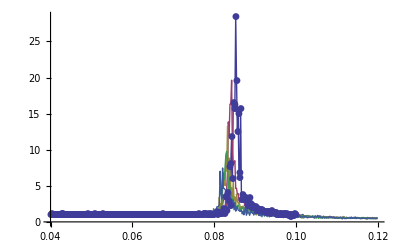

```mathematica
v=9;
ListPlot[{Chi4c[v][5],Chi4c[v][10],Chi4c[v][20],Chi4c[v][30],Chi4c[v][50]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
ListPlot[{Chi4[v][5],Chi4[v][10],Chi4[v][20],Chi4[v][30],Chi4[v][50]},PlotRange->Full,Joined->True,PlotLabel->{"=v  Χ4" v},PlotLegend->{"5k","10k","20k","30k","50"},LegendPosition->{1.1,-0.4},LegendShadow->None,PlotMarkers->Automatic,AxesLabel->{"d","Χ4"}]
```

```mathematica
------------------------------------
```

```mathematica
Do[
Do[
vv=ToString[v];
ll=ToString[l];
Chi4[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized.txt",{Number,Number}];
Chi4t[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top.txt",{Number,Number}];
Chi4f[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-fine.txt",{Number,Number}];
Chi4ft[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-fine.txt",{Number,Number}];

,{v,{5,7,9}}]
,{l,{5,10,20,30,50,100}}]
Do[
Do[
vv=ToString[v];
ll=ToString[l];
Chi4c[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-complete.txt",{Number,Number}];
Chi4ct[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-complete.txt",{Number,Number}];

,{v,{5,7,9}}]
,{l,{5,10,20,30,50}}]
```

```mathematica
ClearAll[Chi11]
```

0.309358  = val

0.06  = d0

0.35  = α

0.08  = z

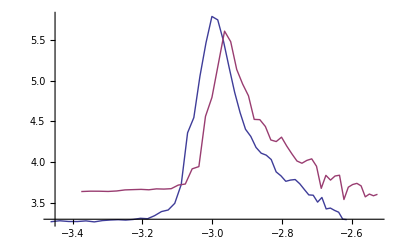

```mathematica
α=0.2;
z=0.2;
d0=0.06;
v=9;
l1=10;
l2=30;
l=0.075+j*0.0004;
val=10000;

Chi11=Chi4f[v][l1][[All,1]];
Chi12=Chi4f[v][l1][[All,2]];
Chi21=Chi4f[v][l2][[All,1]];
Chi22=Chi4f[v][l2][[All,2]];

For[d0=0.06,d0<0.075,d0+=0.001,
For[z=0.08,α≤0.2,α+=0.01,
For[α=0.35,α≤0.65,α+=0.02,

j=1;
While[Chi11[[j]]<d0,j++];
Chil1=Table[{Log[Chi11[[i]]-d0]+z*Log[l1*1000.],
Log[Chi12[[i]]]+α*Log[l1*1000.]},{i,j,Length[Chi11]}];
Chil2=Table[{Log[Chi21[[i]]-d0]+z*Log[l2*1000.],
Log[Chi22[[i]]]+α*Log[l2*1000.]},{i,j,Length[Chi21]}];
Length[Chil2]
Length[Chil1]
i1=Interpolation[Chil1];
i2=Interpolation[Chil2];
min=Max[Log[Chi11[[j]]-d0]+z*Log[l1*1000.],Log[Chi21[[j]]-d0]+z*Log[l2*1000.]];
max=Min[Log[Chi11[[Length[Chi11]]]-d0]+z*Log[l1*1000.],Log[Chi21[[Length[Chi11]]]-d0]+z*Log[l2*1000.]];
delta=(max-min)/50;
int=Sum[delta*(Max[i1[min+k*delta],i2[min+k*delta]]-Min[i1[min+k*delta],i2[min+k*delta]]),{k,0,50}];
If[int<val,
val=int;
d0f=d0;
αf=α;
zf=z;]
]
]
]

" = val"  val
" = d0" d0f
" = α" αf
" = z" zf

Chil1=Table[{Log[Chi11[[i]]-d0f]+zf*Log[l1*1000.],
Log[Chi12[[i]]]+αf*Log[l1*1000.]},{i,1,Length[Chi11]}];
Chil2=Table[{Log[Chi21[[i]]-d0f]+zf*Log[l2*1000.],
Log[Chi22[[i]]]+αf*Log[l2*1000.]},{i,1,Length[Chi21]}];

ListLinePlot[{Chil1,Chil2}]
```

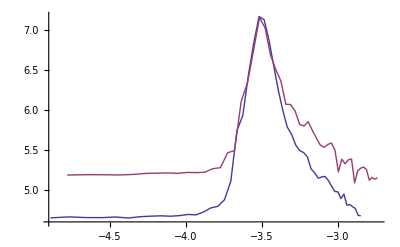

```mathematica
αf=0.5;
zf=0.1;
d0f=0.072;
Chil1=Table[{Log[Chi11[[i]]-d0f]+zf*Log[l1*1000.],
Log[Chi12[[i]]]+αf*Log[l1*1000.]},{i,1,Length[Chi11]}];
Chil2=Table[{Log[Chi21[[i]]-d0f]+zf*Log[l2*1000.],
Log[Chi22[[i]]]+αf*Log[l2*1000.]},{i,1,Length[Chi21]}];

ListLinePlot[{Chil1,Chil2}]
```

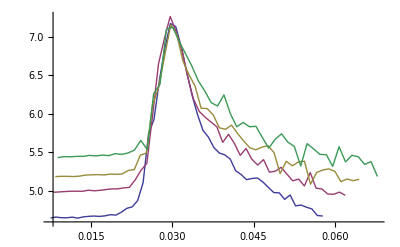

0.072  = d0

0.5  = α

0.1  = z

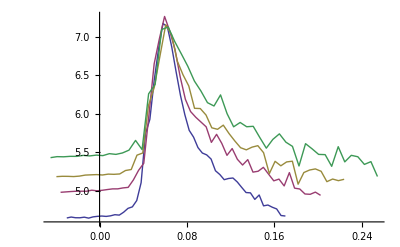

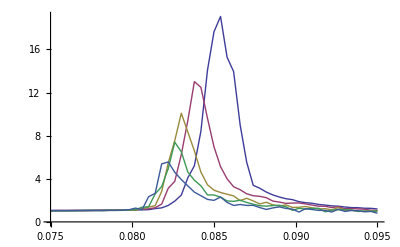

0.078  = d0

0.5  = α

0.25  = z

```mathematica
v=9;
αf=0.5;
zf=0.1;
d0f=0.072;

Do[
chi1=Chi4f[v][l][[All,1]];
chi2=Chi4f[v][l][[All,2]];
chi[l]=Table[{(chi1[[i]]-d0f)*(l*1000.)^zf,
Log[chi2[[i]]]+αf*Log[l*1000.]},{i,1,Length[chi1]}];
,{l,{5,10,20,30,50}}]
ListLinePlot[{chi[10],chi[20],chi[30],chi[50]}]

" = d0" d0f
" = α" αf
" = z" zf
v=9;
αf=0.5;
zf=0.25;
d0f=0.078;

Do[
chi1=Chi4f[v][l][[All,1]];
chi2=Chi4f[v][l][[All,2]];
chi[l]=Table[{(chi1[[i]]-d0f)*(l*1000.)^zf,
Log[chi2[[i]]]+αf*Log[l*1000.]},{i,1,Length[chi1]}];
,{l,{5,10,20,30,50}}]
ListLinePlot[{chi[10],chi[20],chi[30],chi[50]}]
ListLinePlot[{Chi4f[v][5],Chi4f[v][10],Chi4f[v][20],Chi4f[v][30],Chi4f[v][50]},PlotRange->Full]
" = d0" d0f
" = α" αf
" = z" zf
```

0.09  = d0

0.2  = α

0.09  = z

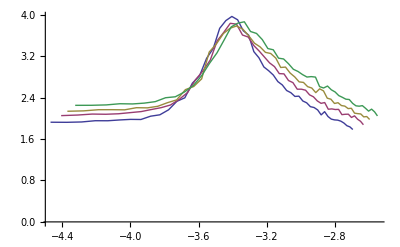

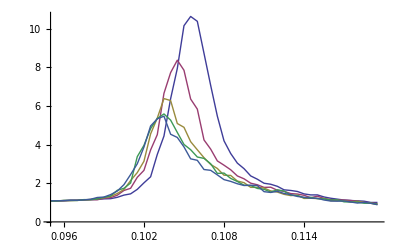

```mathematica
v=7;
αf=0.2;
zf=0.09;
d0f=0.09;

Do[
chi1=Chi4f[v][l][[All,1]];
chi2=Chi4f[v][l][[All,2]];
chi[l]=Table[{Log[chi1[[i]]-d0f]+zf*Log[l*1000.],
Log[chi2[[i]]]+αf*Log[l*1000.]},{i,1,Length[chi1]}];
,{l,{5,10,20,30,50}}]
" = d0" d0f
" = α" αf
" = z" zf
ListLinePlot[{chi[10],chi[20],chi[30],chi[50]}]
ListLinePlot[{Chi4f[v][5],Chi4f[v][10],Chi4f[v][20],Chi4f[v][30],Chi4f[v][50]},PlotRange->Full]
```